90 points

# M154 S13 Lesson 5

## Mario L Gutierrez

## Mathematica Graphics

Mathematica has sophisticated tools for drawing pictures. We already discussed the get coordinates tool  in Lesson 1 under the hearding “The Drawing Tools” . I am not going to describe these tools. Instead read R 5.1.3. EditingMathematicaGraphicsOverview and InteractiveGraphicsPalette .In particular given a plot one can overlay a drawing over the plot. .The drawing tools are not very precise so instead I am going to describe how to construct drawings using Mathematica commands.

Query Graphics. Look at how the picture in the first example is generated.

#### Graphics Primitives

Graphics Primitives are the basic elements from which a picture is drawn. Query Point,Line,Circle,Disk, Polygon and Text.Query Rectangle. A note on Rectangle: when specifying a rectangle you can give any two opposite corners. Thus Rectange[{0,0},{1,1}] and Rectangle[{1,0},{0,1}] give the same image. The Line primitive is of the form Line[{p_1,p_2,... p_n}] and gives what we have (in lesson 2 )  called a broken line. The Point primitive is of the form Point[{x,y}] which gives a point with coordinates {x,y}. We can get a collection of points by Point[{{x1,y1},{x2,y2},...Point{xn,yn}}]

#### Graphics Directives

Graphics Directives are the modifiers of the properties of graphics primitives. Think of graphics primitives as nouns and graphics directives as adjectives. In the option PlotStyle we have seen several graphics directivies e.g. Red,Dotted,Dashing[],Thick,Thickness[]. Query the command Directive.  

I find that in graphics objects readability is improved by grouping adjacent directives in a single Directive. Thus I would do the first example in the query for Graphics as

Here is a variant on the example that gives the same picture

```mathematica
Graphics[{Directive[Thick,Green],Rectangle[{2,-1},{0,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Directive[Purple,Arrowheads[Large]], Arrow[{{4,3/2},{0,3/2},{0,0}}],Directive[Black,Dashed],Line[{{-1,0},{4,0}}]}]
```

### Graphics objects

A Graphics object is list of graphics directives followed by graphics primitives. In a graphics object a graphics directive modifies all of the graphics primitives following it until a new graphics directive is inserted.

Once you have constucted a graphics object you evaluate the command Graphics[] on it to show the graphic. Look at the first example in the document center example for Graphics and be sure you understand it. Graphics takes the same options as Plot and many more.

Notice how the Thick directive is applying to the circle the arrow and the line. We could change this as follows

```mathematica
Graphics[{Directive[Green],Rectangle[{2,-1},{0,1}],Red,Disk[],Directive[Blue,Thick],Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Directive[Thin,Purple,Arrowheads[Large]],Arrow[{{4,3/2},{0,3/2},{0,0}}],Directive[Black,Thickness[.0051],Dashed],Line[{{-1,0},{4,0}}]}]
```

Notice the disc covers the rectangle because Disk is occuring after Rectangle in the graphics object. This is also happening with the circle covering the rectangle,the triangle covering the circle and the line covering the circle.

### Colors

Read S p 100.

Query RGBColor and Hue. We will discuss Manipulate in detail later but the following command shows how the Hue[h] varies as we vary h,

```mathematica
Manipulate[Graphics[{Hue[h],Disk[{0,0},1]},Frame->True],{h,0,1}]
```

Here we are using the Frame option for Graphics.

Query Opacity. The opacity of a color is how transparent it is. For the use of opacity consider the following. We will discuss the Manipulate in detail later, right now we are using the fourth line in the definition.

Notiice that the line primitive has  the points that Mathematica uses to make the broken line that sketches the curve. The red text is a list of options for graphics

### The Epilog and Prolog Options For Graphics

The Epilog→graphicsobj]option in a Plot, ContourPlot or ParametricPlot allows us to overlay a graphic over a plot thus

```mathematica
Plot[Sin[x],{x,-2π,2π},Epilog->{Red,Disk[{1/4,1/4},2/3]},AspectRatio->Automatic,PlotRange->{-2,2}]
```

The Prolog->grapicsobject option allows us to overlay a plot over a graphic thus

```mathematica
Plot[Sin[x],{x,-2π,2π},Prolog->{Red,Disk[{1/4,1/4},2/3]},AspectRatio->Automatic,PlotRange->{-2,2}]
```

Graphics has 69(!) options. Most of them are like the options for Plot and so I will leave you to discover them as needed.

Problem1: Using a command produce the following graphic.  You will definitely neet the Text option, and many of the options from Plot. You want to be careful to align the text so it is above the curve on the left.

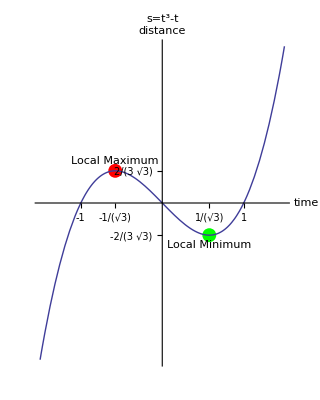

```mathematica
s[t_]:=t^3-t
xval= Table[t,{t,{-1,-1/(√3),1/(√3),1}}];
yval= s[xval];
```

```mathematica
Plot[t^3-t,{t,-1.5,1.5},PlotLabel->Style["s=t^3-t",FontSize->15],AxesLabel->{time,distance},BaseStyle->{FontSize->12},Ticks->{xval,yval},TicksStyle->Directive[Black,10],GridLines->{{xval⟦2⟧,xval⟦3⟧},yval},GridLinesStyle->Directive[Thin,Lighter[Gray]],Prolog->{Red,Disk[{xval⟦2⟧,yval⟦2⟧},1/25],Green,Disk[{xval⟦3⟧,yval⟦3⟧},1/25],Black,Text["Local Maximum",{xval⟦2⟧,.50},BaseStyle->{FontSize->10}],Text["Local Minimum",{xval⟦3⟧,-.50},BaseStyle->{FontSize->10}]},ImageSize->350,AspectRatio->Automatic]
```

12 points

Query PlotLegend. PlotLegend. Also there is a whole packagage devoted to making fancy legends on your plots. You load it with Needs[“PlotLegends`”]

## Show

Query the command Show

The command Show is a very versatile command. It allows us to combine two graphics images in the same picture. In paticular it allows us to combine two plots even if they have different plot domains. See Sp93 Example 4 and example 23 p111 and example 4.9 p115. It also allows us to combine e.g. a Plot with a ContourPlot or a  ParametricPlot. It is important to note that Show has almost as many options as the graphics being combined and these options take precedence over the options in the graphics being combined.

```mathematica
a=Plot[Sin[x],{x,0,8},PlotStyle->Red]
```

```mathematica
b=PolarPlot[θ,{θ,0,8}]
```

```mathematica
Show[a,b,PlotRange->All,AspectRatio->Automatic]
```

Notice that the effects of Prolog and Epilog can also be implemented with Show.

## Manipulate

Query Manipulate Read Manipulate Tutorial The Manipulate command is only touched on briefly in S 129-130 but in much more detail in R Ch 10 and the document center. This is one of the most powerful commands in Mathematica for examing how expressions vary.

When we were dealing with Mathematica’s color schemes we already saw several manipulates of  hue and opacity.

### Geometric Manipulations

Recall the in the transformation a sin(b(x+c))+d that |a| is the amplitude, (2π)/b is the period, c is the phase-shift  and d is the y-shift. Here is an example of a manipulate that uses several sliders (6th line of the query in the document center,and the Manipulate[expr,{{u,u_init,u_lbl},…}]  syntax ( 4th line of the query):

```mathematica
Manipulate[Plot[{Sin[x],a Sin[b(x+c)]+d},{x,-2π,2π},GridLines->Automatic],{{a,.5,"|a|=amplitude"},-1.5,1.5},{{b,1,"2π/b=period"},.5,2},{{c,0,"c=phase-shift"},-1,1},{{d,0,"d=y-shift"},-1,1}]
```

Try clicking the + sign in the upper right hand corner. This lets you run a movie. Try clicking the + sign by  the sliders. This shows you where you are and lets you insert a value.

Observe that the addition of a PlotRange option makes the region we plot over constant, so that the gridlines don’t shift, when we move the sliders to extremes:

```mathematica
Manipulate[Plot[{Sin[x],a Sin[b(x+c)]+d},{x,-2π,2π},GridLines->Automatic,PlotRange->{-2,2}],{{a,.5,"|a|=amplitude"},-1.5,1.5},{{b,1,"2π/b=period"},.5,2},{{c,0,"c=phase-shift"},-1,1},{{d,0,"d=y-shift"},-1,1}]
```

```mathematica
Manipulate[Plot[Tooltip[{Sin[x],a Sin[b(x+c)]+d}],{x,-2π,2π},GridLines->Automatic,PlotRange->{-2,2}],{{a,.5,"|a|=amplitude"},-1.5,1.5},{{b,1,"2π/b=period"},.5,2},{{c,0,"c=phase-shift"},-1,1},{{d,0,"d=y-shift"},-1,1}]
```

Query Axes and Ticks. They are options for the Graphics command

Problem 2 
a: Use Graphics to produce the following graphics image. Don’t forget the text in the lower left hand corner. Hint: You will need the primitives Circle,Line and Text and the options Axes and Ticks.

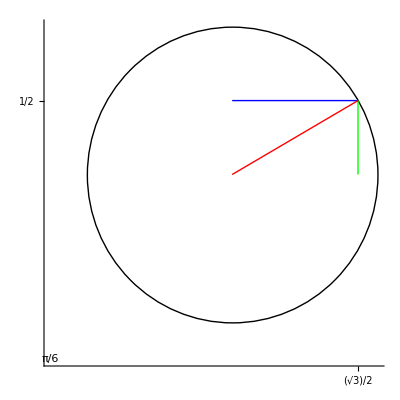

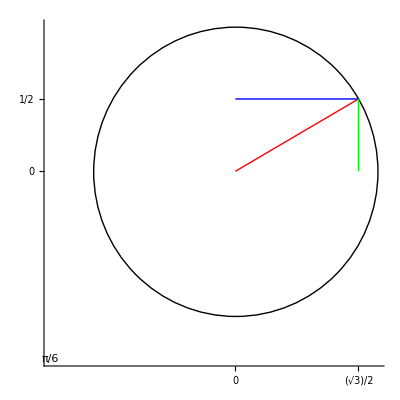

```mathematica
Graphics[{Circle[{0,0}],Red,Line[{{0,0},{(√3)/2,1/2}}],Blue,Line[{{0,1/2},{(√3)/2,1/2}}],Green,Line[{{(√3)/2,0},{(√3)/2,1/2}}],Directive[Black,Thick],Text[π/6,{-1.3,-1.3}]},Ticks ->{{0,(√3)/2},{0,1/2}},Axes->True]
```

12 points

Problem 3: a: Produce the following Manipulate. Use the Manipulate[expr,{u,u_min,u_max,du}] syntax.

```mathematica
Manipulate[Graphics[{Circle[{0,0}],Red,Line[{{0,0},{Cos[θ],Sin[θ]}}],Blue,Line[{{0,Sin[θ]},{Cos[θ],Sin[θ]}}],Green,Line[{{Cos[θ],0},{Cos[θ],Sin[θ]}}],Directive[Black,Thick],Text[θ,{-1.3,-1.3}]},Ticks ->{{Cos[θ],0},{0,Sin[θ]}},Axes->True],{θ,0,2 π,π/12}]
```

12 points.

```mathematica
θvals=Union[Table[m,{m,0,2π,π/4}],Table[θ,{θ,0,2π,π/6}]]
```

{0,π/6,π/4,π/3,π/2,(2 π)/3,(3 π)/4,(5 π)/6,π,(7 π)/6,(5 π)/4,(4 π)/3,(3 π)/2,(5 π)/3,(7 π)/4,(11 π)/6,2 π}

Problem 3 b Use the list θval and the Manipulate[expr,{u,{u_1,u_2,…}}] syntax to produce the following manipulate:

```mathematica
Manipulate[Graphics[{Circle[{0,0}],Red,Line[{{0,0},{Cos[θ],Sin[θ]}}],Blue,Line[{{0,Sin[θ]},{Cos[θ],Sin[θ]}}],Green,Line[{{Cos[θ],0},{Cos[θ],Sin[θ]}}],Directive[Black,Thick],Text[θ,{-1.3,-1.3}]},Ticks ->{{Cos[θ],0},{0,Sin[θ]}},Axes->True],{θ,θvals,PopupMenu}]
```

12 points

Notice the difference between the two Manipulates. The first give us a slider and the second gives a pull down menu.

Manipulate can be used to vary any Mathematica expression not just geometric expressions. In the tutorial read In[7] to In[13].

## 3 Dimensions

#### A Reconsideration Of CountourPlot.

A contour of a function in two variable, e.g. f(x,y)=z  is the curve f(x,y)=c for some constant c. Equivalently this is the projection into the x,y plane of the intersection of the graph of the plane z=c .

The general Mathematica command ContourPlot contours of f shaded accourding to the value of c with lower heights shaded from dark blue through lighter shades of blue according to the value of z.

```mathematica
example[x_,y_]:=x^4-x^2+y^2
```

```mathematica
ContourPlot[example[x,y],{x,-2,2},{y,-2,2}]
```

As seen in lesson 5 we use contour plot with an equation

```mathematica
ContourPlot[example[x,y]==0,{x,-2,2},{y,-2,2}]
```

```mathematica
ContourPlot[example[x,y]==-1/10,{x,-2,2},{y,-2,2}]
```

```mathematica
ContourPlot[example[x,y]==1/10,{x,-2,2},{y,-2,2}]
```

```mathematica
Manipulate[ContourPlot[example[x,y]==c,{x,-2,2},{y,-2,2}],{{c,0},-1/10,1/10}]
```

```mathematica
Manipulate[ContourPlot[example[x,y]==c,{x,-2,2},{y,-2,2}],{{c,0},-1/10,1/10,1/100}]
```

##### Manipulate vs. ListPlot

Notice that if we play the Manipulate the curve is drawn with fewer points and we get broken lines although when we release the slider the curve reverts to smooth. This is because Mathematica has to do computation each time we move the slider. This is akin to showing  a movie where we have to stop and draw the animation as we show each frame. More sensible is to draw the frames at once and then show the movie. The next command is asking that we compute 100 ContourPlots so it will take some time to execute

```mathematica
alist=Table[ContourPlot[example[x,y]==c,{x,-2,2},{y,-2,2}],{c,-1/10,1/10,1/1000}];
```

Query ListAnimate animating lists.

```mathematica
ListAnimate[alist]
```

```mathematica
ListAnimate[alist,10]
```

Here we have computed all of the ContourPlots beforhand and then are playing the movie of our pre-computed frames.

Let’s return to lesson 4.

```mathematica
hypotrochoid[a_,b_,h_,t_]:={(a-b)Cos[t]+h Cos[(a-b)/b t],(a-b)Sin[t]-h Sin[(a-b)/b t]}
```

I made a mistake in the last problem set. The period of the hypotrochoid is 2π Numerator[b/(a-b)]

```mathematica
epitrochoid[a_,b_,h_,t_]:={(a+b)Cos[t]+h Cos[(a+b)/b t],(a+b)Sin[t]-h Sin[(a+b)/b t]}
```

I made a mistake in the last problem set. The period of the epitrochoid is 2π Numerator[b/(a+b)]

Let’s try a Manipulate with the hypotrochoid

```mathematica
Manipulate[ParametricPlot[hypotrochoid[1,1/4,1/4,t],{t,0,c 2π},PlotRange->{{-2,2},{-2,2}}],{c,.001,1}]
```

```mathematica
Manipulate[ParametricPlot[hypotrochoid[1,2,1,t],{t,0,c 4π},PlotRange->{{-2,2},{-2,2}}],{c,.001,1}]
```

Problem4 Make a function msph[a_,b_,h_]  that manipulates the tracing of the hypotrochoid. Your PlotRange  should be:

{{-(a+b+h+1/4),a+b+h+1/4},{-(a+b+h+1/4),a+b+h+1/4}}

```mathematica
msph[1,1/4,1/4]
```

```mathematica
msph[1/3,7/5,2]
```

```mathematica
msph[a_,b_,h_]:=Manipulate[ParametricPlot[{(a-b)Cos[t]+h Cos[(a-b)/b t],(a-b)Sin[t]-h Sin[(a-b)/b t]},{t,0,c 2 π},PlotRange->{{-(a+b+h+1/4),a+b+h+1/4},{-(a+b+h+1/4),a+b+h+1/4}}],{c,.001,1}]
```

Your parameter domain is wrong because you haven’t accounted for the period. Go back and read the text in red about the periods

```mathematica
msph[1,1/4,1/4]
```

Notice the movie above gets jagged.

8 points

Problem5: Make a function fah[a_,b_,h_] using ListAnimate which gives a movie of smooth curves. Hint Wrap ListAnimate around a Table of ParametricPlots. Here are two tests to try:

```mathematica
fah[1,1/4,1/4]
```

```mathematica
fah[1/3,7/5,2]
```

```mathematica
fah[a_,b_,h_]:=ListAnimate[Table[ParametricPlot[{(a-b)Cos[c t]+h Cos[(a-b)/b c t],(a-b)Sin[c t]-h Sin[(a-b)/b c t]},{t,0,4π},PlotRange->{{-(a+b+h+1/4),a+b+h+1/4},{-(a+b+h+1/4),a+b+h+1/4}}],{c,0,1,.001}],80]
```

```mathematica
fah[1,1/4,1/4]
```

Even though showing two revolutions ( {t,0,4π} ) on the graph above is quite useless (at least for our purpose), it does make the following graph somewhat more interesting.

```mathematica
fah[1/3,7/5,2]
```

8 points same problem with periodicity.

## 3D Plotting

Just as Mathematica has three commands Plot, ContourPlot, and ParametricPlot. There are three commands for  plotting in 3-dimensions. Read s 5.1-5.3.Query Plot3D,ContourPlot3D, and ParametricPlot3D. As usual be sure to read the details and options sections

### Plot3D

Example 1: The upper half-Sphere

```mathematica
upper=Plot3D[√(1-x^2-y^2),{x,-2,2},{y,-2,2}]
```

Removing Distortion: The x and y axes are 4 times the length of the z-axis so ...

```mathematica
Plot3D[√(1-x^2-y^2),{x,-2,2},{y,-2,2},BoxRatios->{1,1,1/4}]
```

```mathematica
Plot3D[{-√(1-x^2-y^2),√(1-x^2-y^2)},{x,-2,2},{y,-2,2},BoxRatios->{1,1,1/2}]
```

We give a much more sophisticated plot: Read torus . The torus is usually described implicitly or as a parametrized surface but we can write z as an explicit function of x and y

```mathematica
Plot3D[√(1-(5-√(x^2+y^2))^2),{x,-6,6},{y,-6,6},PlotRange->{-1.2,1.2}]
```

```mathematica
Plot3D[{√(1-(5-√(x^2+y^2))^2),-√(1-(5-√(x^2+y^2))^2)},{x,-6,6},{y,-6,6},PlotRange->{-1.2,1.2}]
```

#### Two classic examples from multi-variate calculus

##### Problem6 A function which is differentiable every where but the origin, where it is discontinuous

Consider the following surface

-Graphics3D-

It seems like the function plotted on this graph is that of (x y)/(x^2+y^2).

right

Rotate the plot until you can see the curve generated by the intersection of the curve with the plane x=0 what is the equation of this curve?

f(x,y) = 0

Almost. f(x,y)=0 is the complement of the origin in the union of the x-axis and the y-axis. A curve is specified by a pair of equations, in this case:i x=0,z=0 that is the y-axis. Recall curves are given implicitly by h(x,y,z)=0,k(x,y,z}=0 in this case  h(x,y,z)=x,k(x,y,z)=z

What is the curve cut out by the plane y=0?

f(x,y) = 0

see answers. y=0,z=0 As above you want the x-axis which should be visible when you rotate

What is the curve cut out by the plane x=y?

f(x,y) = y^2/(y^2+y^2)=1/y^2=1/x^2

see answers. x=y,z=1/2

What is the curve cut out by the plane x=-y?

f(x,y) = -y^2/((-y)^2+y^2)=-1/y^2=-1/x^2

see answers. It is the line x=-y,z=-1/2

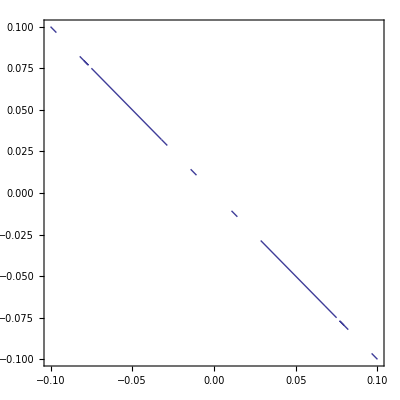

```mathematica
ContourPlot[f[x,y]==-1/2,{x,-1/10,1/10},{y,-1/10,1/10}]
```

Wrong

b: Plot the function f(x,y)=(x y)/(x^2+y^2) on the rectangle -1/10<x<1/10,-1/10<y<1/10 with PlotPoints->200

For the above see answers

```mathematica
Plot3D[(x y)/(x^2+y^2),{x,-1/10,1/10},{y,-1/10,1/10},PlotPoints->200]
```

What does the surface seem to be doing over (0,0)?

The graph goes to infinity as we approach (0,0).

No it does not.

c : what is the value of f(x,y) on the  line making the angle θ with the positive x-axis? (Hint try working in polar coordinates)

f(x,y)=g(r,θ)=(r Cos[θ]r Sin[θ])/((r Cos[θ])^2+(r Sin[θ])^2)=(r^2 Cos[θ]Sin[θ])/(r^2 (Cos[θ]^2+Sin[θ]^2))=Cos[θ]Sin[θ]=1/2 Sin[2θ]

This shows f is bounded above by 1/2 and below by -1/2

I’ll give your 4 points for getting this right.

d: Why is 0 not a removable discontinuity of f?

0 is not a removable discontinuity because the graph goes to infinity as it gets close to that point (there is no single hole in the graph).

see answers. It is not a removable discontinuity because the limit varies according to which direction (given by θ) you approach (0,0}

Look at the following

```mathematica
f[x_,y_]:=(x y)/(x^2+y^2)
```

```mathematica
Plot3D[f[x,y],{x,-.1,.1},{y,-.1,.1},AxesOrigin->{0,0,0}]
```

-Graphics3D-

You should be able to see all the lines I discussed. and the bounds. The pinch over (0,0) is the evidence of discontinuity.

4 points

##### Problem 7 A differentiable function whose mixed partials are not equal

```mathematica
Clear[nm,dx,dy,d2xy,d2yx]
```

Set

```mathematica
nm[x_,y_]:=(x y (x^2-y^2))/(x^2+y^2)
```

the function nm is not defined at (0,0). We define it to be 0 at (0,0).

We compute

```mathematica
D[nm[x,y],x]
```

and define

```mathematica
dx[x_,y_]=-(2 x^2 y (x^2-y^2))/((x^2+y^2)^2)+(2 x^2 y)/(x^2+y^2)+(y (x^2-y^2))/(x^2+y^2)
```

```mathematica
D[nm[x,y],y]
```

```mathematica
dy[x_,y_]=-(2 x y^2 (x^2-y^2))/((x^2+y^2)^2)-(2 x y^2)/(x^2+y^2)+(x (x^2-y^2))/(x^2+y^2)
```

Notice that dx and dy are not defined at (0,0).

In order to compute ∂_x nm(0,0) we work directly

```mathematica
Limit[nm[x,0]/x,x->0]
```

I am going to lead you through a proof that dx is continuous at 0. I am going to do this by showing that as ϵ→0 ,dx→0 on the punctured ball of radius ϵ around (0.0). Let's work in polar coordinates.

```mathematica
dxrt=dx[x,y]/.{x->r Cos[θ],y->r Sin[θ]}
```

```mathematica
Simplify[dxrt]
```

Thus on the punctured ball |dx|≤4ϵ

Similarly we compute directly that dy is 0 at (0,0) and dy is continuous at (0,0). By second year calculus nm is differentiable at (0,0) with Jacobian derivative 0.

We have

```mathematica
D[nm[x,y],x,y]
```

```mathematica
d2xy[x_,y_]=(8 x^2 y^2 (x^2-y^2))/((x^2+y^2)^3)-(2 x^2 (x^2-y^2))/((x^2+y^2)^2)-(2 y^2 (x^2-y^2))/((x^2+y^2)^2)+(2 x^2)/(x^2+y^2)-(2 y^2)/(x^2+y^2)+(x^2-y^2)/(x^2+y^2)
```

```mathematica
D[nm[x,y],y,x]
```

```mathematica
d2yx[x_,y_]=(8 x^2 y^2 (x^2-y^2))/((x^2+y^2)^3)-(2 x^2 (x^2-y^2))/((x^2+y^2)^2)-(2 y^2 (x^2-y^2))/((x^2+y^2)^2)+(2 x^2)/(x^2+y^2)-(2 y^2)/(x^2+y^2)+(x^2-y^2)/(x^2+y^2)
```

It looks like we must have equality of mixed partials but this is only away from (0,0). These expressions are undefined at 0. Notice these expressions are homogeneous or degree 0 so they are constant along open line segments from the origin to a non-zero point

a: Prove that there is no definition of d2xy and d2yx at (0,0) that makes these two functions continuous at 0. Hint Use polar coordinates as  in the problem above

```mathematica
{d2xy[x,y],d2yx[x,y]}/.{x->r Cos[θ],y->r Sin[θ]}
```

```mathematica
Simplify[%]
```

We cannot use the definition of a punctured ball to prove contuinity in this case since the radius r cancels out as we simplify our coordinates.

see answers

b:Plot d2xy. Can you see evidence of a discontinuity?

```mathematica
Plot3D[d2yx[x,y],{x,-5,5},{y,-5,5},BoxRatios->{1/2,1/2,1/4}]
```

It can easily be seen that the surface curls up and displays a discontuinity at the origin.

c: Inequality of mixed partials. We have

```mathematica
dx[x,y]
```

And we have dx(0,0)=0

We have

∂_(x,y) nm(0,0)=lim_(y→0) (dx(0,y)-0)/y

Compute this limit

```mathematica
Limit[dx[0,y]/y,y->0]
```

■We have

∂_(y,x) nm(0,0)=lim_(x→0) (dy(x,0)-0)/x

Compute this limit.

```mathematica
Limit[dy[x,0]/x,x->0]
```

The partials are not equal, hence it has been shown that the function is not of class C^2.

8 points

We can see this in a plot. We use the 3D graphics primitive Line[{{a_x,a_y,a_z},{b_x,b_y,b_z}}]

```mathematica
plot=Plot3D[nm,{x,-1/10,1/10},{y,-1/10,1/10}]
```

```mathematica
xaxis=Graphics3D[{Directive[Green,Thick],Line[{{-1/10,0,0},{1/10,0,0}}]}]
```

```mathematica
yaxis=Graphics3D[{Directive[Red,Thick],Line[{{0,-1/10,0},{0,1/10,0}}]}]
```

```mathematica
Show[plot,xaxis,yaxis]
```

Notice that as we walk away from the origin in the positive y-direction the slopes in the x-direction get more and more negative. Similarly is we walk away from the origin in the positive x-direction the slopes in the y direction get more and more positive. Thus

∂_(x,y) nm(0,0)≤0,∂_(y,x) nm(0,0)≥0

If they in fact exist. We have shown that they exist and are -1 and 1 respectively.

#### ContourPlot3D

Surfaces can be given as the locus of an equation in three variables. We plot these surfaces using ContourPlot3D

```mathematica
ContourPlot3D[x^2+y^2+z^2==1,{x,-2,2},{y,-2,2},{z,-2,2}]
```

```mathematica
ContourPlot3D[x^2+y^2+z^2,{x,-10,10},{y,-10,10},{z,-10,10},Contours->4]
```

##### The torus as a contour

```mathematica
ContourPlot3D[(5-√(x^2+y^2))^2+z^2==1,{x,-6,6},{y,-6,6},{z,-2,2}]
```

#### Parametric Curves and Surfaces.ParametricPlot3D

Query ParametricPlot3D, S p138 and ParametricPlot3D.

Let’s parametrize the torus:  We parametrize the circle in the plane by

(R Cos(θ),R Sin(θ),0),0≤ϕ<2π

We want to take a circle determined by the vectors

(r Cos(θ),r Sin(θ),0)  and(0,0,r). For a fixed θ this circle is given by Cos(ϕ)(r Cos(θ),r Sin(θ),0) +Sin(ϕ)(0,0,r), 0≤ϕ<2π.

Translating this circle so that it has center (R Cos(θ),R Sin(θ),0) we get, adding the three vectors,

(R Cos(θ),R Sin(θ),0)+ Cos(ϕ)(r Cos(θ),r Sin(θ),0) +Sin(ϕ)(0,0,r) which is the vector

( (R+r Cos(ϕ))Cos(θ),(R+r Cos(ϕ))Sin(θ) ,r Sin(ϕ))

So lets look at some parametric plots:

R>r

R=5,r=2

```mathematica
ParametricPlot3D[{(5+2Cos[ϕ])Cos[θ],(5+2Cos[ϕ])Sin[θ],2 Sin[ϕ]},{θ,0,2π},{ϕ,0,2π}]
```

R=r

R=2

```mathematica
ParametricPlot3D[{(2+2Cos[ϕ])Cos[θ],(2+2Cos[ϕ])Sin[θ],2 Sin[ϕ]},{θ,0,2π},{ϕ,0,2π}]
```

Let’s look at the upper half of this torus

```mathematica
ParametricPlot3D[{(2+2Cos[ϕ])Cos[θ],(2+2Cos[ϕ])Sin[θ],2 Sin[ϕ]},{θ,0,2π},{ϕ,0,π}]
```

R<r

R=2,r=5

As above we’ll look at the upper half:

```mathematica
ParametricPlot3D[{(2+5Cos[ϕ])Cos[θ],(2+5Cos[ϕ])Sin[θ],5 Sin[ϕ]},{θ,0,2π},{ϕ,0,π}]
```

Observe that the torus is also generated by rotating a circle around the z-axis. If that circle is centered on the origin (R=0) we get a sphere

R=0

R=0,r=2

```mathematica
ParametricPlot3D[{(2Cos[ϕ])Cos[θ],(2Cos[ϕ])Sin[θ],2Sin[ϕ]},{θ,0,2π},{ϕ,0,2π}]
```

The angular parametrization of the circle

Suppose R=0 then we only have to rotate the circle of radius r halfway around the radius of rotation and we get

```mathematica
ParametricPlot3D[{(2Cos[ϕ])Cos[θ],(2Cos[ϕ])Sin[θ],2Sin[ϕ]},{θ,0,π},{ϕ,0,2π}]
```

If we want to see half:

```mathematica
ParametricPlot3D[{(2Cos[ϕ])Cos[θ],(2Cos[ϕ])Sin[θ],2Sin[ϕ]},{θ,0,π},{ϕ,0,π}]
```

#### Parametrized Curves: The torus knot

Let m,n be relatively prime integers>1. The  (m,n) torus knot is the map of the circle which wraps n times  around the circle in the interior of the torus while it  goes around the axis of revolution m times.

Problem 8

a: Parametrize the (m,n) torus knot

```mathematica
torusknot[m_,n_]:={(m+Cos[n t]) Cos[m t],(m+Cos[n t]) Sin[m t],Sin[n t]}
```

see answers

b: Now plot the (2, 3) torus knot make it Red and Thick.

```mathematica
ParametricPlot3D[torusknot[2,3], {t, 0, 2 π},PlotStyle->{Red,Thick}]
```

-Graphics3D-

c: Show this knot wrapped around it’s a torus

```mathematica
torus3D[m_,n_]:={(m+Cos[n ϕ])Cos[m θ],(m+Cos[n ϕ])Sin[m θ],Sin[n ϕ]}
ParametricPlot3D[torus3D[2,3],{θ,0,2π},{ϕ,0, 2π}]
```

-Graphics3D-

4 points

Notice that the plot of the 2-3 knot seems to have three crossings. This is because we are projecting a three dimensional object into a two dimensional space. We can add a Hue to the curve where the argument of the Hue varies from 0 to 4/5 as z varies from -2 to 3

```mathematica
ParametricPlot3D[{(5 + 2 Cos[3 t]) Cos[2 t], (5 + 2 Cos[3 t]) Sin[2 t], 2 Sin[3 t]}, {t, 0, 2 π},ColorFunction->(Hue[(#3+2)/5]&),PlotStyle->Thick]
```

The difference in Hues at the crossings show the z-coordinates are different at the crossings so that as a 3 dimensional curve there are no crossings!